```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Estimator Parameters: Length of Wilson Lines:*)
L:=10
(*Number of Time Steps:*)
n:=10
(*Distance between instanton and anti-instanton*)
R:=5
(*Distance between quark and anti-quark*)
r:=1
(*Integration Bounds*)
l:=15
```

```mathematica
η:=Array[Eta,{4,4,3}]
Do[Eta[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Eta[4,4,a]=0,{a,1,3}]
Do[Eta[k,4,a]=KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Eta[4,k,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
ηbar:=Array[Etabar,{4,4,3}]
Do[Etabar[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Etabar[4,4,a]=0,{a,1,3}]
Do[Etabar[k,4,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Etabar[4,k,a]=+KroneckerDelta[k,a],{k,1,3},{a,1,3}]
```

```mathematica
(*Define instanton solutions
Areg[γ2_,ρ_,t_]:=t/(t^2+γ2+ρ^2)
Aanti[γ2_,ρ_,t_]:=t/(t^2+γ2+ρ^2)*)
```

```mathematica
(*Test Values*)
θtest={θ3->1.,θ1->0.,θ2->1.,θ4->1.,θ5->1.,θ6->0.};
ypoint={1.,1.,0.,0.};
rottest=Rot[{Sqrt[2]/2,Sqrt[2]/2,0,0},{0,0,Sqrt[2]/2,Sqrt[2]/2}];
```

```mathematica
(*Instanton rotation*)
Rvec:=
R{0,0,0,1}
(*2 unit vectors will specify a plane and its dual to be rotated around*)
(*u1={Sin[θ1]Sin[θ2]Sin[θ3],Sin[θ3]Sin[θ2]Cos[θ1],Sin[θ3]Cos[θ2],Cos[θ3]}
u2={Sin[θ4]Sin[θ5]Sin[θ6],Sin[θ4]Sin[θ5]Cos[θ6],Sin[θ4]Cos[θ5],Cos[θ6]}
u1.u2/.θtest
A=Sum[LeviCivitaTensor[4][[i]][[j]]u1[[i]]u2[[j]],{i,1,4},{j,1,4}]
AntisymmetricMatrixQ[A]
th1=Eigenvalues[A][[2]]/I;
th2=Eigenvalues[A][[4]]/I;
Eigenvalues[A]/.θtest
A1=1/(th1(th2^2-th1^2))(th2^2A+A.A.A)
A2=1/(th2(th1^2-th2^2))(th1^2A+A.A.A)*)
```

```mathematica
(*Ratio Ansatz*)
Ya[y_]:=y+Rvec/2
Yi[y_]:=y-Rvec/2
Arot[y_]:=Table[Sum[(ηbar[[μ,ν,aa]]*Yi[y][[ν]]*Ya[y].Ya[y]+η[[μ,ν,aa]]*Ya[y][[ν]]*Yi[y].Yi[y])/((Yi[y].Yi[y])(Ya[y].Ya[y])+Yi[y].Yi[y]+Ya[y].Ya[y]),{ν,1,4}],{μ,1,4},{aa,1,3}]
Dimensions[Arot[ypoint]]
```

{4,3}

```mathematica
(*Wilson Line at a point in time*)
W2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]]+I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]]
Wd2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]]-I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]]
```

```mathematica
(*Table of wilson lines along L*)
WList[y_,rot_]:=Table[W2[Arot[y+rot.{0,0,0,(i-1/2)L/n}]],{i,1,n}]
WdList[y_,rot_]:=Table[Wd2[Arot[y+rot.{0,0,0,(i-1/2)L/n}]],{i,1,n}]
```

```mathematica
(*Matrix Product*)
Wapprox[y_,rot_]:=Dot@@WList[y,rot] (* applies the function to everything in the table *)
Wdapprox[y_,rot_]:=Dot@@WdList[y,rot]
```

```mathematica
(*Upper and Lower Lines for B fields*)
WApproxUpper[y_,rot_,t_]:=Dot@@Table[W2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,t,n}]
WApproxLower[y_,rot_,t_]:=Dot@@Table[W2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,1,t}]
WdApproxUpper[y_,rot_,t_]:=Dot@@Table[Wd2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,t,n}]
WdApproxLower[y_,rot_,t_]:=Dot@@Table[Wd2[Arat[y+{0,0,0,(i-1/2)L/n}]],{i,1,t}]
```

```mathematica
Imes[y_,rot_,rr_]:=1-1/2*Tr[Wapprox[y,rot].Wdapprox[y-rot.{rr,0,0,0},rot]](* integrand *)
```

```mathematica
(*0.22 seconds and 1.36 for rotating wilson lines*)
(*0.078 seconds and 1.36 for rotating field*)
Timing[Imes[ypoint,rottest,5]]
```

$Aborted

```mathematica
(*Obtaining random spherically distributed points.*)
RandSphere:=Module[{r,poi},r=2;
While[r>1,
poi=RandomReal[{-1,1},4];
r=Norm[poi]]; 
poi=poi/r;
poi ]
{RandSphere,RandSphere}
(*ListPlot[Table[randSphere,100],AspectRatio->1]*)
```

{{-0.0478779,0.814439,-0.163588,0.554649},{0.594044,-0.000970057,-0.689855,-0.413777}}

```mathematica
(*Random sampling of rotation matricies*)
RotR[a_]:=
{{a[[1]],-a[[2]],-a[[3]],-a[[4]]},
{a[[2]],a[[1]],-a[[4]],a[[3]]},
{a[[3]],a[[4]],a[[1]],-a[[2]]},
{a[[4]],-a[[3]],a[[2]],a[[1]]}};
RotL[p_]:={{p[[1]],-p[[2]],-p[[4]],-p[[3]]},
{p[[2]],p[[1]],p[[3]],-p[[4]]},
{p[[4]],-p[[3]],p[[1]],p[[2]]},
{p[[3]],p[[4]],-p[[2]],p[[1]]}};
Rot[a_,p_]:=RotL[a].RotR[p]
RandRot:=Rot[RandSphere,RandSphere]
```

```mathematica
RandY:=Append[RandomReal[{-l,l},3],0]
```

```mathematica
(*0.05-0.1 for rotating the lines*)
(*Similar range for rotating the fields*)
Timing[Imes[RandY,RandRot,5]]
```

{0.078125,0.00292402+0. ⅈ}

```mathematica
(*Number of test points for monte carlo*)
num=1000;
l=15;
```

```mathematica
(*Random numbers for all future points*)
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];
```

```mathematica
(*Error of Monte Carlo*)
8l^3/num*Sum[Imes[randY[[5+1,i]],randRot[[5+1,i]],5],{i,1,num}]
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];
8l^3/num*Sum[Imes[randY[[5+1,i]],randRot[[5+1,i]],5],{i,1,num}]
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];8l^3/num*Sum[Imes[randY[[5+1,i]],randRot[[5+1,i]],5],{i,1,num}]
```

347.789+0. ⅈ

209.505+0. ⅈ

233.113+0. ⅈ

```mathematica
(*Unit conversion to GeV and multiplication by instanton density*)
units=25.5
```

25.5

```mathematica
DistanceDataMes=Table[{rr,units*8l^3/num*Sum[Imes[randY[[rr/2+1,i]],randRot[[rr/2+1,i]],rr],{i,1,num}]},{rr,0,20,2}]
```

{{0,43.7363+0. ⅈ},{2,64.7107+0. ⅈ},{4,193.025+0. ⅈ},{6,245.558+0. ⅈ},{8,221.498+0. ⅈ},{10,231.015+0. ⅈ},{12,247.831+0. ⅈ},{14,237.266+0. ⅈ},{16,214.732+0. ⅈ},{18,166.23+0. ⅈ},{20,132.671+0. ⅈ}}

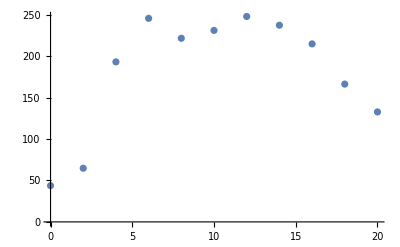

```mathematica
PlotMes=ListPlot[DistanceDataMes]
```

```mathematica
(*Field Strength*)
Fmunu=Table[D[Arat[{y[1],y[2],y[3],y[4]}][[mu]][[a]],y[nu] ]-D[Arat[{y[1],y[2],y[3],y[4]}][[nu]][[a]],y[mu] ],{mu,1,4},{nu,1,4},{a,1,3}]+Table[
-Sum[
LeviCivitaTensor[3][[a,b,c]]Arat[{y[1],y[2],y[3],0}][[mu]][[b]]Arat[{y[1],y[2],y[3],0}][[nu]][[c]],{b,1,3},{c,1,3}],
{mu,1,4},{nu,1,4},{a,1,3}];
B[y1_,y2_,y3_,t_]:=Table[1/2Sum[LeviCivitaTensor[3][[i]][[j]][[k]](Fmunu[[j]][[k]][[a]]/.{y[1]->y1,y[2]->y2,y[3]->y3,y[4]->t})PauliMatrix[a] ,{j,1,3},{k,1,3},{a,1,3}],{i,1,3}]
```

```mathematica
B[ypoint[[1]],ypoint[[2]],ypoint[[3]],1][[1]]/.{θ3->1.,θ1->0,θ2->0}
```

{{0.0161029,0.121208-0.0326775 ⅈ},{0.121208+0.0326775 ⅈ,-0.0161029}}

```mathematica
(*Integrand for two B fields*)
ImesBB[y1_,y2_,y3_,t1_,t2_]:=Sum[Tr[WApproxLower[{y1,y2,y3,0},t1].B[y1,y2,y3,t1][[i]].WApproxUpper[{y1,y2,y3,0},t1].WdApproxUpper[{y1-r,y2,y3,0},t2].B[y1,y2,y3,t1][[i]].WdApproxLower[{y1-r,y2,y3,0},t2]],{i,1,3}]
```

```mathematica
AbsoluteTiming[ImesBB[ypoint[[1]],ypoint[[2]],ypoint[[3]],1,1]/.{θ3->1.,θ1->0,θ2->0}]
```

{0.326356,0.0569468+0. ⅈ}

```mathematica
DistanceDataMesBB=Table[{θ3,Sum[(L/n)^2*NIntegrate[1/(2Pi^2)Sin[θ3]^2Sin[θ2]ImesBB[y1,y2,y3,t1,t2],{θ1,0,2Pi},{θ2,0,Pi},{y1,-l,l},{y2,-l,l},{y3,-l,l},AccuracyGoal->2],{t1,1,n},{t2,1,n}]},{θ3,0,Pi,Pi/4}]
```

$Aborted

```mathematica
ListPlot[AngleDataMesBB]
```

```mathematica
(*SU(3) matrix for baryon*)
Wapprox3[y_,rot_]:=SparseArray[ArrayFlatten[{{Wapprox[y,rot],0},{0,1}}]]
```

```mathematica
(*Baryon Integrand-Direct Triangle*)
Ibar[y_,rot_,rr_]:=1+1/6(LeviCivitaTensor[3].Wapprox3[y-rot.{0,0,1/Sqrt[2]*rr,0},rot][[1]].Wapprox3[y-rot.{1/Sqrt[2]*rr,0,0,0},rot][[2]].Wapprox3[y-rot.{0,1/Sqrt[2]*rr,0,0},rot][[3]]+
LeviCivitaTensor[3].Wapprox3[y-rot.{0,0,1/Sqrt[2]*rr,0},rot][[3]].Wapprox3[y-rot.{1/Sqrt[2]*rr,0,0,0},rot][[1]].Wapprox3[y-rot.{0,1/Sqrt[2]*rr,0,0},rot][[2]]+LeviCivitaTensor[3].Wapprox3[y-rot.{0,0,1/Sqrt[2]*rr,0},rot][[2]].Wapprox3[y-rot.{1/Sqrt[2]*rr,0,0,0},rot][[3]].Wapprox3[y-rot.{0,1/Sqrt[2]*rr,0,0},rot][[1]]-
LeviCivitaTensor[3].Wapprox3[y-rot.{0,0,1/Sqrt[2]*rr,0},rot][[1]].Wapprox3[y-rot.{1/Sqrt[2]*rr,0,0,0},rot][[3]].Wapprox3[y-rot.{0,1/Sqrt[2]*rr,0,0},rot][[2]]-
LeviCivitaTensor[3].Wapprox3[y-rot.{0,0,1/Sqrt[2]*rr,0},rot][[2]].Wapprox3[y-rot.{1/Sqrt[2]*rr,0,0,0},rot][[1]].Wapprox3[y-rot.{0,1/Sqrt[2]*rr,0,0},rot][[3]]-LeviCivitaTensor[3].Wapprox3[y-rot.{0,0,1/Sqrt[2]*rr,0},rot][[3]].Wapprox3[y-rot.{1/Sqrt[2]*rr,0,0,0},rot][[2]].Wapprox3[y-rot.{0,1/Sqrt[2]*rr,0,0},rot][[1]])
```

```mathematica
Timing[Ibar[{100,0,0,0},RandRot,5]]
```

{0.359375,2.5287×10^-8+5.29396×10^-23 ⅈ}

```mathematica
num=1000;
```

```mathematica
8l^3/num*Sum[Ibar[randY[[5+1,i]],randRot[[5+1,i]],5],{i,1,num}]
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];
8l^3/num*Sum[Ibar[randY[[5+1,i]],randRot[[5+1,i]],5],{i,1,num}]
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];8l^3/num*Sum[Ibar[randY[[5+1,i]],randRot[[5+1,i]],5],{i,1,num}]
```

101.276-2.98833×10^-16 ⅈ

126.297-1.4687×10^-15 ⅈ

114.526-8.03343×10^-16 ⅈ

```mathematica
DistanceDataBar=Table[{rr,units*l^3/num*Sum[Ibar[randY[[rr/2+1,i]],randRot[[rr/2+1,i]],rr],{i,1,num}]},{rr,0,20,2}]
```

{{0,3.93435×10^-13+0. ⅈ},{2,49.918-1.07245×10^-16 ⅈ},{4,184.133+3.93324×10^-16 ⅈ},{6,282.722+9.16311×10^-16 ⅈ},{8,258.313-5.12362×10^-16 ⅈ},{10,325.672+1.78957×10^-17 ⅈ},{12,346.408-3.8025×10^-16 ⅈ},{14,313.862+3.77468×10^-16 ⅈ},{16,286.493-3.01768×10^-16 ⅈ},{18,249.49-7.93204×10^-17 ⅈ},{20,265.684+2.52598×10^-16 ⅈ}}

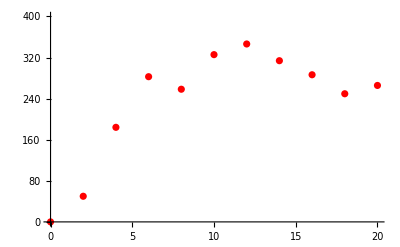

```mathematica
PlotBar=ListPlot[DistanceDataBar,PlotRange->{0,400},PlotStyle->Red]
```

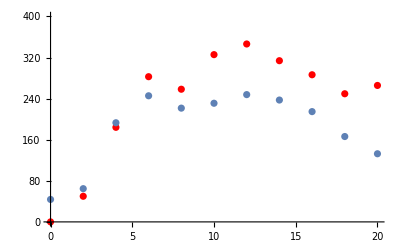

```mathematica
Show[PlotBar, PlotMes]
```

```mathematica
Wdapprox3[y_,rot_]:=SparseArray[ArrayFlatten[{{Wapprox[y,rot],0},{0,1}}]]
```

```mathematica
TetraStructure[wd1_,wd2_,wd3_,wd4_]=Permute[{wd1,wd2,wd3,wd4},SymmetricGroup[4]]
```

{{wd1,wd2,wd3,wd4},{wd1,wd2,wd4,wd3},{wd1,wd3,wd2,wd4},{wd1,wd3,wd4,wd2},{wd1,wd4,wd2,wd3},{wd1,wd4,wd3,wd2},{wd2,wd1,wd3,wd4},{wd2,wd1,wd4,wd3},{wd2,wd3,wd1,wd4},{wd2,wd3,wd4,wd1},{wd2,wd4,wd1,wd3},{wd2,wd4,wd3,wd1},{wd3,wd1,wd2,wd4},{wd3,wd1,wd4,wd2},{wd3,wd2,wd1,wd4},{wd3,wd2,wd4,wd1},{wd3,wd4,wd1,wd2},{wd3,wd4,wd2,wd1},{wd4,wd1,wd2,wd3},{wd4,wd1,wd3,wd2},{wd4,wd2,wd1,wd3},{wd4,wd2,wd3,wd1},{wd4,wd3,wd1,wd2},{wd4,wd3,wd2,wd1}}

```mathematica
Wdvars[y_,rot_,rr_]:={Wdapprox3[y,rot],Wdapprox3[y+{rr,0,0,0},rot],Wdapprox3[y+{0,rr,0,0},rot],Wdapprox3[y+{0,0,rr,0},rot]}
```

```mathematica
(TetraStructure@@(Wdvars[RandY,RandRot,5]))[[1,1]]
```

SparseArray[…]

```mathematica
Itetra[y_,rot_,rr_]:=1-1/(24*3^4)*Sum[Tr[Wapprox3[y,rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,1]]]Tr[Wapprox3[y+{rr,0,0,0},rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,2]]]Tr[Wapprox3[y+{0,rr,0,0},rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,3]]]Tr[Wapprox3[y+{0,0,rr,0},rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,4]]],{i,1,24}]
```

```mathematica
AbsoluteTiming[Itetra[0,RandRot,0]]
```

{24.0004,0.238155+0. ⅈ}

```mathematica
num=100
```

100

```mathematica
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];
```

```mathematica
8l^3/num*Sum[Itetra[randY[[5+1,i]],randRot[[5+1,i]],5],{i,1,num}]
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];
8l^3/num*Sum[Itetra[randY[[5+1,i]],randRot[[5+1,i]],5],{i,1,num}]
randRot=Table[RandRot,11,num];
randY=Table[RandY,11,num];8l^3/num*Sum[Itetra[randY[[5+1,i]],randRot[[5+1,i]],5],{i,1,num}]
```

285.178+1.64404×10^-16 ⅈ

380.19+4.34851×10^-16 ⅈ

313.398-2.5268×10^-16 ⅈ

```mathematica
DistanceDataTetra=Table[{rr,l^3/num*Sum[Itetra[randY[[rr/2+1,i]],randRot[[rr/2+1,i]],rr],{i,1,num}]},{rr,0,20,2}]
```

{{0,221.942+0. ⅈ},{2,287.467-6.36019×10^-17 ⅈ},{4,324.485-3.84447×10^-17 ⅈ},{6,274.969-2.97889×10^-17 ⅈ},{8,189.001-1.90213×10^-16 ⅈ},{10,235.61-2.42636×10^-16 ⅈ},{12,289.236-3.05355×10^-16 ⅈ},{14,178.536-8.24822×10^-16 ⅈ},{16,203.514-1.40206×10^-16 ⅈ},{18,135.131-8.64395×10^-17 ⅈ},{20,96.4279-1.06337×10^-16 ⅈ}}

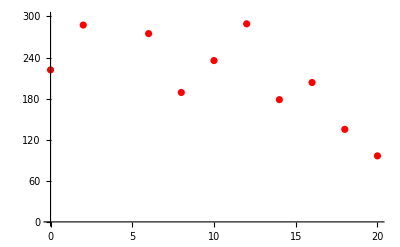

```mathematica
PlotTetra=ListPlot[Re[DistanceDataTetra],PlotRange->{0,300},PlotStyle->Red]
```